Magdalena Waligórska, Klaudia Składanek, inżynieria biomedyczna A2
zadanie 1 zestaw 24

```mathematica
ff[x_]:=6
```

Funkcje kształtu:

```mathematica
fi1[x_, x1_, x2_]:=(x-x2)/(x1-x2)
fi2[x_, x1_, x2_]:=(x-x1)/(x2-x1)
```

Forma dwuliniowa:

```mathematica
bb[v_, u_, x_]:= -(2x v+x^2 D[v, x])D[u, x]- (D[u, x]+x^2u)v
```

Definicje macierzy lokalnych:

```mathematica
x1=.; x2=.;
a[1, 1]= ∫_x1^x2 bb[fi1[x, x1, x2], fi1[x, x1, x2], x]ⅆx;
a[1, 2]= ∫_x1^x2 bb[fi1[x, x1, x2], fi2[x, x1, x2], x]ⅆx;
a[2, 1]= ∫_x1^x2 bb[fi2[x, x1, x2], fi1[x, x1, x2], x]ⅆx;
a[2, 2]= ∫_x1^x2 bb[fi2[x, x1, x2], fi2[x, x1, x2], x]ⅆx;
```

Definicje lokalnych wektorów prawych stron:

```mathematica
b[1] = ∫_x1^x2 ff[x]*fi1[x,x1,x2]ⅆx;
b[2] = ∫_x1^x2 ff[x]*fi2[x,x1,x2]ⅆx;
```

Określenie początku (ax) i końca (bx) przedziału oraz jego podziału na elementy (nnp) uwzględniając liczbę iteracji:

```mathematica
{ ax =3, bx = 9};
iter = If[iter > 0, iter+1, 1, 1]
nnp = If[OddQ[iter],5*iter,5*(iter-1)+1]
ddx = (bx-ax)/(nnp -1);
```

10

46

Wyzerowanie macierzy globalnej (aa) i głównego wektora przwych stron(bw):

```mathematica
Do[{bw[kw] = 0, Do[{aa[kw, kk] = 0}, {kk, 0, nnp+1}]}, {kw, 0, nnp+1}]
```

Agragacja macierzy globalnej i głównego wektora prawych stron:

```mathematica
Do[{x2 = ax+ddx ne, 
x1 = x2 - ddx,
bw[ne] = Simplify[bw[ne]+b[1]], 
bw[ne+1] = Simplify[bw[ne+1] + b[2]],
aa[ne, ne] = aa[ne, ne] + a[1, 1],
aa[ne, ne+1] = aa[ne, ne+1] + a[1,2],
aa[ne+1, ne] = aa[ne+1, ne] + a[2,1],
aa[ne+1, ne+1] = aa[ne+1, ne+1] + a[2,2]},
{ne, 1, nnp-1}]
```

```mathematica
MatrixForm[Array[aa, {nnp, nnp}]];
```

```mathematica
MatrixForm[Array[bw, {nnp}]];
```

Określenie warunków brzegowych:

```mathematica
{aa[1,0] = -9,
aa[0,0] = 0,
aa[0,1] = 1,
aa[nnp, nnp+1]= 81,
aa[nnp+1, nnp]= 1,
aa[nnp+1, nnp+1]= 0};
{bw[0] = 7,
bw[nnp+1]=-2};
```

Prezentacja macierzy globalnej i głównego wektora prawych stron wraz z warunkami brezgowymi:

```mathematica
AA = Array[aa, {nnp+2, nnp+2}, {0,0}];
MatrixForm[AA];
```

```mathematica
BW = Array[bw, {nnp+2}, 0];
MatrixForm[BW];
```

Obliczenie współczynników funkcji przybliżającej:

```mathematica
wsp = LinearSolve[N[AA],BW]
```

Określenie postaci funkcji przybliżającej:

```mathematica
vv[x_, x1_, x2_, x3_]:= If[x>x1 && x<x2,(x-x1)/(x2-x1),0] + If[x>x2 && x<x3, (x-x3)/(x2-x3),0]
```

Określenie postaci funkcji przybliżającej:

```mathematica
up[x_]:= ∑_(k=0)^(nnp-1) wsp[[k+2]]vv[x, ax+(k-1)ddx, ax+k ddx,ax+(k+1)ddx]
```

```mathematica
funk[iter]= up[x];
```

Przedstawienie wykresu funkcji przybliżającej dla danego podziału oraz podziału poprzedniego:

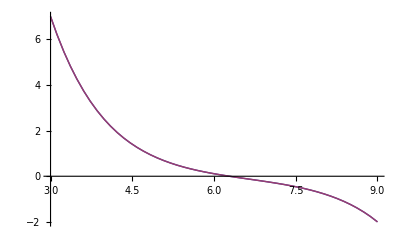

```mathematica
If[iter >1,Plot[{funk[iter],funk[iter-1]}, {x, 3, 9}],0]
```

Obliczanie różnicy pomiędzy rozwiązaniami różniącymi się liczbą podziałów o 1 oraz jej graficzne przedstawienie:

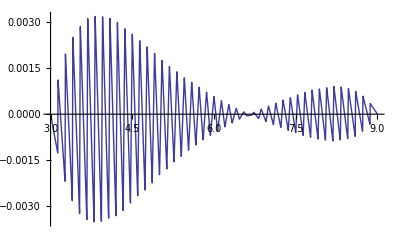
{-Graphics-,{6,0.413414}
{16,0.0257006}
{26,0.00838334}
{36,0.00413786}
{46,0.00246464}}

```mathematica
If[OddQ[iter],0,
{Plot[funk[iter]-funk[iter-1],{x, 3, 9}],
blad[iter/2] =√N[∫_ax^bx (funk[iter]-funk[iter-1])^2 ⅆx];
ile[iter/2] = nnp;
Aile = Array[ile, iter/2];
Ablad = Array[blad, iter/2];
Column[Transpose[{Aile, Ablad}]]}]
```

Wybierając coraz mniejsze przedziały otrzymujemy coraz mniejsze różnice pomiędzy kolejnymi rozwiązaniami; możemy więc przypuszczać, że obliczona funkcja jest zbieżna do rozwiązania dokładnego.